```mathematica
M[a_, b_, c_,d_]:= {{a,b}, {c,d}} + IdentityMatrix[2]
MMM [a_, b_, c_,d_]:= KroneckerProduct[M[a,b,c,d],M[a,b,c,d],M[a,b,c,d]]
CZ = DiagonalMatrix[{1,1,1,-1,1,-1,-1,-1}]
CZMMM[a_, b_, c_,d_] := CZ.MMM[a,b,c,d]
K[a_,b_] := a.b - b.a
w = E^(2*I*Pi/3)
basis ={{1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1},{0,1/Sqrt[3],1/Sqrt[3],0,1/Sqrt[3],0,0,0},{0,0,0,1/Sqrt[3],0,1/Sqrt[3],1/Sqrt[3],0},{0,1/Sqrt[3],w^2/Sqrt[3],0,w^1/Sqrt[3],0,0,0},{0,0,0,1/Sqrt[3],0,w^1/Sqrt[3],w^2/Sqrt[3],0},{0,1/Sqrt[3],w^1/Sqrt[3],0,w^2/Sqrt[3],0,0,0},{0,0,0,1/Sqrt[3],0,w^2/Sqrt[3],w^1/Sqrt[3],0}}
Mbasis = basis[[1;;4,All]]
Mwbasis = basis[[5;;6, All]]
(*Mproj = ConjugateTranspose[Mbasis].Mbasis
Mwproj = ConjugateTranspose[Mwbasis].Mwbasis*)
PBasis = {{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}, {0,0,1/Sqrt[2],0,1/Sqrt[2],0,0,0},
{0,0,0,1/Sqrt[2],0,1/Sqrt[2],0,0},{0,0,1/Sqrt[2],0,-1/Sqrt[2],0,0,0},{0,0,0,1/Sqrt[2],0,-1/Sqrt[2],0,0}}
P1Basis = PBasis[7;;8,All]
(*Pproj  = ConjugateTranspose[P1Basis].P1Basis*)
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

ⅇ^((2 ⅈ π)/3)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1/(√3) | 1/(√3) | 0 | 1/(√3) | 0 | 0 | 0
0 | 0 | 0 | 1/(√3) | 0 | 1/(√3) | 1/(√3) | 0
0 | 1/(√3) | ⅇ^(-(2 ⅈ π)/3)/(√3) | 0 | ⅇ^((2 ⅈ π)/3)/(√3) | 0 | 0 | 0
0 | 0 | 0 | 1/(√3) | 0 | ⅇ^((2 ⅈ π)/3)/(√3) | ⅇ^(-(2 ⅈ π)/3)/(√3) | 0
0 | 1/(√3) | ⅇ^((2 ⅈ π)/3)/(√3) | 0 | ⅇ^(-(2 ⅈ π)/3)/(√3) | 0 | 0 | 0
0 | 0 | 0 | 1/(√3) | 0 | ⅇ^(-(2 ⅈ π)/3)/(√3) | ⅇ^((2 ⅈ π)/3)/(√3) | 0)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1/(√3) | 1/(√3) | 0 | 1/(√3) | 0 | 0 | 0
0 | 0 | 0 | 1/(√3) | 0 | 1/(√3) | 1/(√3) | 0)

(0 | 1/(√3) | ⅇ^(-(2 ⅈ π)/3)/(√3) | 0 | ⅇ^((2 ⅈ π)/3)/(√3) | 0 | 0 | 0
0 | 0 | 0 | 1/(√3) | 0 | ⅇ^((2 ⅈ π)/3)/(√3) | ⅇ^(-(2 ⅈ π)/3)/(√3) | 0)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1/(√2) | 0 | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 1/(√2) | 0 | 1/(√2) | 0 | 0
0 | 0 | 1/(√2) | 0 | -1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 1/(√2) | 0 | -1/(√2) | 0 | 0)

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{0,0,1/(√2),0,1/(√2),0,0,0},{0,0,0,1/(√2),0,1/(√2),0,0},{0,0,1/(√2),0,-1/(√2),0,0,0},{0,0,0,1/(√2),0,-1/(√2),0,0}}[7;;8,All]

Here, we will show all 5 things that can be generated in the Symmetric basis; X, Y, Z, ZXZ, and ZYZ (all with an I prefactor):
(We will ignore the identity matrix, because it commutes with everything, thus won’t help us generate anything)

```mathematica
{MatrixForm[MA= (Normal[Series[Simplify[Mbasis.CZMMM[0,0,0,0].CZMMM[0,I*a,I*a,0].ConjugateTranspose[Mbasis]],{a,0,1}]]-IdentityMatrix[4])/a],
MatrixForm[MB=(Normal[Series[Simplify[Mbasis.CZMMM[0,0,0,0].CZMMM[0,a,-a,0].ConjugateTranspose[Mbasis]],{a,0,1}]]-IdentityMatrix[4])/a],
MatrixForm[MC=(Normal[Series[Simplify[Mbasis.CZMMM[0,0,0,0].CZMMM[I*a,0,0,-I*a].ConjugateTranspose[Mbasis]],{a,0,1}]]-IdentityMatrix[4])/a],
MatrixForm[MD=(Normal[Series[Simplify[Mbasis.CZMMM[0,I*a,I*a,0].CZMMM[0,0,0,0].ConjugateTranspose[Mbasis]],{a,0,1}]]-IdentityMatrix[4])/a],
MatrixForm[ME=(Normal[Series[Simplify[Mbasis.CZMMM[0,a,-a,0].CZMMM[0,0,0,0].ConjugateTranspose[Mbasis]],{a,0,1}]]-IdentityMatrix[4])/a]}
```

{(0 | 0 | ⅈ √3 | 0
0 | 0 | 0 | ⅈ √3
ⅈ √3 | 0 | 0 | 2 ⅈ
0 | ⅈ √3 | 2 ⅈ | 0),(0 | 0 | √3 | 0
0 | 0 | 0 | -√3
-√3 | 0 | 0 | 2
0 | √3 | -2 | 0),(3 ⅈ | 0 | 0 | 0
0 | -3 ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 0 | ⅈ √3 | 0
0 | 0 | 0 | ⅈ √3
ⅈ √3 | 0 | 0 | -2 ⅈ
0 | ⅈ √3 | -2 ⅈ | 0),(0 | 0 | √3 | 0
0 | 0 | 0 | -√3
-√3 | 0 | 0 | -2
0 | √3 | 2 | 0)}

```mathematica
(*{MatrixForm[XA= (Normal[Series[Simplify[Mbasis.CZMMM[0,0,0,0].CZMMM[0,I*a,I*a,0].ConjugateTranspose[Mbasis]],{a,0,1}]]-IdentityMatrix[4])/a],
MatrixForm[XB=(Normal[Series[Simplify[Mbasis.CZMMM[0,0,0,0].CZMMM[0,a,-a,0].ConjugateTranspose[Mbasis]],{a,0,1}]]-IdentityMatrix[4])/a],
MatrixForm[XC=(Normal[Series[Simplify[Mbasis.CZMMM[0,0,0,0].CZMMM[I*a,0,0,-I*a].ConjugateTranspose[Mbasis]],{a,0,1}]]-IdentityMatrix[4])/a],
MatrixForm[XD=(Normal[Series[Simplify[Mbasis.CZMMM[0,I*a,I*a,0].CZMMM[0,0,0,0].ConjugateTranspose[Mbasis]],{a,0,1}]]-IdentityMatrix[4])/a],
MatrixForm[XE=(Normal[Series[Simplify[Mbasis.CZMMM[0,a,-a,0].CZMMM[0,0,0,0].ConjugateTranspose[Mbasis]],{a,0,1}]]-IdentityMatrix[4])/a]}
IH = KroneckerProduct[IdentityMatrix[2],HadamardMatrix[2]]
MA = IH .XA.IH
MB = IH.XB.IH
MC = IH.XC.IH
MD = IH.XD.IH
ME = IH.XE.IH*)
```

MG MI and MJ below let us do SU(2) on the third and fourth states;

```mathematica
{MatrixForm[MF=(MA + MD)/(2*Sqrt[3])],
MatrixForm[MG=(MA - MD)/4],
MatrixForm[MH=(MB +ME)/(2*Sqrt[3])],
MatrixForm[MI=(MB - ME)/4],
MatrixForm[MJ=K[MG,MI]/2],
MatrixForm[MK=(MC + MJ)/3],
MatrixForm[ML = MI + MJ],
MatrixForm[MM = K[ML,MH]],
MatrixForm[MN = MM - MF],
MatrixForm[MO=K[MF+MG+MH,MI+MK]+ MM-2*MJ-MH]
}
```

{(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -ⅈ | 1
0 | 0 | -1 | ⅈ),(0 | 0 | ⅈ | -1
0 | 0 | -1 | ⅈ
ⅈ | 1 | 0 | 0
1 | ⅈ | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)}

```mathematica
{MatrixForm[iXI = MF], MatrixForm[MG], MatrixForm[iYZ =MH], MatrixForm[MI], MatrixForm[MJ], MatrixForm[MK], MatrixForm[iYX = -K[MF, MG]], MatrixForm[iYY = K[MF, MI]], MatrixForm[K[MH, K[MF, MG]]/2-MI], MatrixForm[K[ MH, K[MF, MI]]/2+MG]}
```

{(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

```mathematica
{MatrixForm[iZX = K[iYX, iXI] ],MatrixForm[iZY = K[iYY, iXI]],MatrixForm[iZZ = K[iYZ, iXI]]}
```

{(0 | 2 ⅈ | 0 | 0
2 ⅈ | 0 | 0 | 0
0 | 0 | 0 | -2 ⅈ
0 | 0 | -2 ⅈ | 0),(0 | -2 | 0 | 0
2 | 0 | 0 | 0
0 | 0 | 0 | 2
0 | 0 | -2 | 0),(2 ⅈ | 0 | 0 | 0
0 | -2 ⅈ | 0 | 0
0 | 0 | -2 ⅈ | 0
0 | 0 | 0 | 2 ⅈ)}

```mathematica
MatrixExp[iXI*a]
```

(Cos[a] | 0 | ⅈ Sin[a] | 0
0 | Cos[a] | 0 | ⅈ Sin[a]
ⅈ Sin[a] | 0 | Cos[a] | 0
0 | ⅈ Sin[a] | 0 | Cos[a])

```mathematica
MatrixExp[MG*a]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | Cos[a] | ⅈ Sin[a]
0 | 0 | ⅈ Sin[a] | Cos[a])

```mathematica
MatrixExp[MJ* a]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | ⅇ^(-ⅈ a) | 0
0 | 0 | 0 | ⅇ^(ⅈ a))

```mathematica
{MatrixForm[MatrixExp[iYX * a]],MatrixForm[MatrixExp[iZZ * a]],MatrixForm[MatrixExp[iYZ * a]]}
```

{(Cos[a] | 0 | 0 | Sin[a]
0 | Cos[a] | Sin[a] | 0
0 | -Sin[a] | Cos[a] | 0
-Sin[a] | 0 | 0 | Cos[a]),(ⅇ^(2 ⅈ a) | 0 | 0 | 0
0 | ⅇ^(-2 ⅈ a) | 0 | 0
0 | 0 | ⅇ^(-2 ⅈ a) | 0
0 | 0 | 0 | ⅇ^(2 ⅈ a)),(Cos[a] | 0 | Sin[a] | 0
0 | Cos[a] | 0 | -Sin[a]
-Sin[a] | 0 | Cos[a] | 0
0 | Sin[a] | 0 | Cos[a])}

```mathematica
ClearAll["Global`*"]
```

```mathematica
MatrixForm[Normal[Series[Simplify[Mbasis.CZMMM[a,b,c,d].ConjugateTranspose[Mbasis]],{a,0,1},{b,0,1},{c,0,1}, {d,0,1}]]]
```

(1+3 a | 0 | √3 b+2 √3 a b | 0
0 | -1-3 d | 0 | c (-√3-2 √3 d)
√3 c+2 √3 a c | 0 | 1+2 b c+d+a (2+2 b c+2 d) | b (2+2 d)+a b (2+2 d)
0 | b (-√3-2 √3 d) | c (-2-2 d)+a c (-2-2 d) | -1+b c (-2-2 d)+a (-1-2 d)-2 d)

```mathematica
MatrixForm[Normal[Series[Simplify[PBasis.CZMMM[0,0,0,a].ConjugateTranspose[PBasis]],{a,0,1}]]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1+a | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1-2 a | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1-3 a | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1+a | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1-2 a | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1+a | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1-2 a)

```mathematica
MatrixForm[Simplify[(Mwproj).(Pproj).(Mwproj).(Pproj)]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ/(4 √3) | 0 | ⅈ/(4 √3) | 0 | 0 | 0
0 | 0 | 1/12 (1+(-1)^(1/3)) | 0 | 1/12 (-1-(-1)^(1/3)) | 0 | 0 | 0
0 | 0 | 0 | 1/12 (1-(-1)^(2/3)) | 0 | 1/12 (-1+(-1)^(2/3)) | 0 | 0
0 | 0 | 1/12 (-1+(-1)^(2/3)) | 0 | 1/12 (1-(-1)^(2/3)) | 0 | 0 | 0
0 | 0 | 0 | 1/12 (-1-(-1)^(1/3)) | 0 | 1/12 (1+(-1)^(1/3)) | 0 | 0
0 | 0 | 0 | ⅈ/(4 √3) | 0 | -ⅈ/(4 √3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

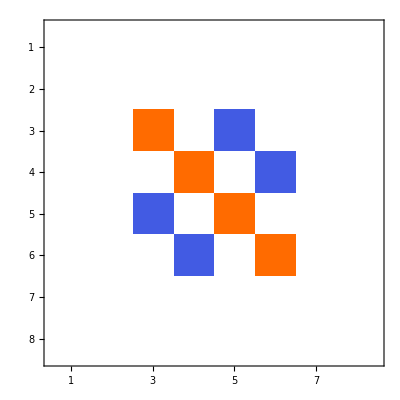

```mathematica
MatrixPlot[%404]
```